```mathematica
hill[x_,n_] := x^n/(1+x^n)
input = 0.4;
steadypar[n_, hillweight_]:=Sort[{r,s}/.NSolve[{input - r + s * hillweight * hill[r * s,n] == 0, input - s + r * hillweight * hill[r * s,n] == 0,r≥0,s≥0}, {r, s},Reals]]
ModelSolver[σ_,τ_,hillweight_,tmax_,sigend_]:=NDSolve[{r'[t]==input+Piecewise[{{σ,t<sigend},{0,t≥0.5}}]-r[t-τ]+s[t]*hillweight*hill[r[t]*s[t],2],s'[t]==input-s[t-τ]+r[t]*hillweight*hill[r[t]*s[t],2],r[t/;t≤0]==First[steadypar[2,hillweight]][[1]],s[t/;t≤0]==First[steadypar[2,hillweight]][[2]],integral'[t]==r[t]-s[t],integral[t/;t≤0]==0},{r,s,integral},{t,0,tmax}]
prob[p_] := 1/(1 + ⅇ^(p))
```

```mathematica
populations = Manipulate[Plot[Evaluate[({r[x],s[x]}/.ModelSolver[σ, τ, 1,tmax, 0.5][[1]])],{x,0,tmax},PlotRange->{rmin, rmax},  Frame -> True, FrameLabel -> {"t[s]", "r(t)"}, PlotLegends->Placed[{"r1(t)", "r2(t)"}, {0.85, 0.8}]], {τ, 0, 2.5, 0.1}, {σ, 0 , 4, 0.01}, {rmin,0,5,0.01},{rmax,0,5,0.01}, {tmax, 10, 200, 15}]
```

```mathematica
probabilities = Manipulate[Plot[Evaluate[({prob[- β * integral[x]], prob[β * integral[x]]}/.ModelSolver[σ, τ, 1,tmax, 0.5][[1]])],{x,0,tmax},PlotRange->{pmin, pmax}, Frame -> True, FrameLabel -> {"t[s]", "p(t)"}, PlotLegends->Placed[{"p1(t)", "p2(t)"}, {0.85, 0.8}]], {τ, 0, 3, 0.05}, {σ, 0 , 4, 0.001}, {β, 1, 1.2, 0.01},{pmin,0,1,0.01},{pmax,0,1,0.01}, {tmax, 10, 200, 15}]
```

```mathematica
(* Populations and probabilities on connected plots *)
merge = Manipulate[{Plot[Evaluate[({r[x],s[x]}/.ModelSolver[σ, τ, 1,tmax, 0.5][[1]])],{x,0,tmax},PlotRange->{0, 1.5}, Frame -> True,   FrameLabel -> {"t[s]", "r(t)"}, PlotLegends->{"r1(t)", "r2(t)"}], Plot[Evaluate[({prob[- β * integral[x]], prob[β * integral[x]]}/.ModelSolver[σ, τ, 1,tmax, 0.5][[1]])],{x,0,tmax},PlotRange->{0, 1}, Frame -> True, FrameLabel -> {"t[s]", "p(t)"}, PlotLegends->{"p1(t)", "p2(t)"}]}, {τ, 0, 2.5, 0.1}, {σ, 0 , 4, 0.01}, {β, 1, 1.2, 0.01},  {tmax, 10, 200, 15},SaveDefinitions->True]
```

```mathematica
(* Probabilities with abs of difference *)
probabilities = Manipulate[Plot[Evaluate[({prob[- β * integral[x]], prob[β * integral[x]], Abs[ 2 * prob[β * integral[x]]- 1]}/.ModelSolver[σ, τ, 1,tmax, 0.5][[1]])],{x,0,tmax},PlotRange->{pmin, pmax}, Frame -> True, FrameLabel -> {"t[s]", "p(t)"}, PlotLegends->Placed[{"p1(t)", "p2(t)"}, {0.85, 0.8}]], {τ, 0, 3, 0.05}, {σ, 0 , 4, 0.001}, {β, 1, 1.2, 0.01},{pmin,0,1,0.01},{pmax,0,1,0.01}, {tmax, 10, 200, 15}]
```

```mathematica
(* Populations and probabilities on connected plots with dependence on end time of sigma /sigend/*)
merge = Manipulate[{Plot[Evaluate[({r[x],s[x]}/.ModelSolver[σ, τ, 1,tmax, sigend][[1]])],{x,0,tmax},PlotRange->{0, 1.5}, Frame -> True,   FrameLabel -> {"t[s]", "r(t)"}, PlotLegends->{"r1(t)", "r2(t)"}], Plot[Evaluate[({prob[- β * integral[x]], prob[β * integral[x]]}/.ModelSolver[σ, τ, 1,tmax, sigend][[1]])],{x,0,tmax},PlotRange->{0, 1}, Frame -> True, FrameLabel -> {"t[s]", "p(t)"}, PlotLegends->{"p1(t)", "p2(t)"}]}, {τ, 0, 2.5, 0.1}, {σ, 0 , 4, 0.01}, {β, 1, 1.2, 0.01},  {tmax, 10, 200, 15}, {sigend, 0, 20, 0.1},SaveDefinitions->True]
```

```mathematica
(* PLOTS OF CERTAINTY *)
righttime =8;
p[t_, σ_, τ_, β_] := prob[β * (First[integral/.ModelSolver[σ,τ,1,righttime,0.5]])[t]]
certainty[σ_, τ_, β_] := NMaximize[{Abs[2 * p[t, σ, τ, β] - 1],0≤t≤righttime}, t]
```

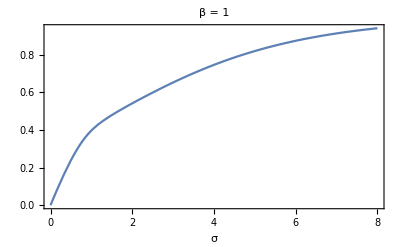

```mathematica
Plot[First[certainty[σ, 1.7, 1]], {σ, 0, 8},Frame -> True,  FrameLabel -> {"σ", " "}, PlotLabel-> "β = 1"]
```

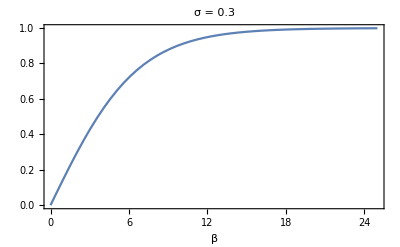

```mathematica
Plot[First[certainty[0.3, 1.7, β]], {β, 0, 25}, Frame -> True, FrameLabel -> {"β", " "}, PlotLabel-> "σ = 0.3"]
```

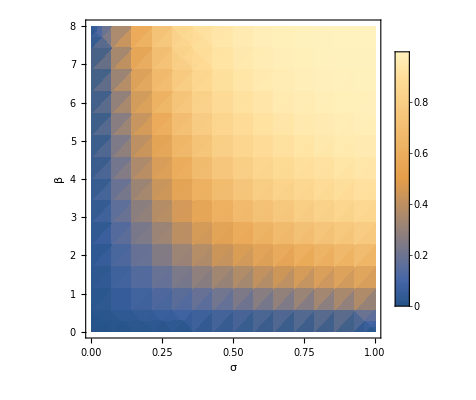

```mathematica
DensityPlot[First[certainty[σ, 1.7, β]], {σ, 0,1},  {β,0, 8}, PlotLegends->Automatic,  FrameLabel -> {"σ", "β"}]
```